```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3+c04 x^4, 0≤x≤1/2}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3+c14(x-1)^4, 1/2<x≤3/2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Continuity*)
C1l=Simplify[h[x],0≤x≤1/2]/.x->1/2
C1r=Simplify[h[x],1/2<x≤3/2]/.x->1/2
C2l=Simplify[h[x],1/2<x≤3/2]/.x->3/2
```

1+c01/2+c02/4+c03/8+c04/16

1/2 (-c11+1/2 (c12+1/2 (-c13+c14/2)))

1/2 (c11+1/2 (c12+1/2 (c13+c14/2)))

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[∑_(i=-3)^3 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-3)^3 i f[x-i],x>0&&x<1/2],x]
```

{1,c01,c02+2 c12,c03,c04+2 c14}

{0,-2 c11,0,-2 c13}

```mathematica
(*Smoothness*)
S0=Simplify[D[h[x],x],0<x<1/2]/.x->0
S1l=Simplify[D[h[x],x],0<x<1/2]/.x->1/2
S1r=Simplify[D[h[x],x],1/2<x<3/2]/.x->1/2
S2l=Simplify[D[h[x],x],1/2<x<3/2]/.x->3/2
```

c01

c01+1/2 (2 c02+1/2 (3 c03+2 c04))

c11+1/2 (-2 c12+1/2 (3 c13-2 c14))

c11+1/2 (2 c12+1/2 (3 c13+2 c14))

```mathematica
GenSols=Solve[{
	C1l==C1r,
	C2l==0,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T0[[5]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0,
	S0==0,
	S1l==S1r,
	S2l==0
	},
	{c01,c02,c03,c04,c11,c12,c13,c14}
]
```

{{c01→0,c02→-3,c03→0,c04→4,c11→-1/2,c12→3/2,c13→0,c14→-2}}

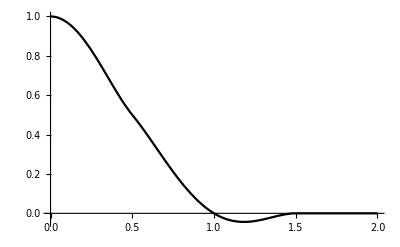

```mathematica
Plot[f[x]/.GenSols[[1]],{x,0,2},PlotStyle->Black]
```

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
```

```mathematica
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>3-1/2&&y<4-1/2]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-3-1/2&&y<-2-1/2]
}];
```

```mathematica
TableForm[{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}]
TableForm[{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}]
```

1/8 (2 (-1+x) x (1+2 x)^2 y (1-3 y+4 y^3)+(-1+x) x (1+2 x)^2 (-1+y) y (1+2 y)^2 φ^2+x (1-3 x+4 x^3) y (1-3 y+4 y^3) φ^2+4 (1-3 x^2+4 x^4) (1-3 y^2+4 y^4) φ^2+2 (1-3 x^2+4 x^4) y (1-3 y+4 y^3) (-1-2 φ+φ^2)+2 (-1+x) x (1+2 x)^2 (1-3 y^2+4 y^4) (-1-2 φ+φ^2))
1/8 (2 (x+3 x^2-4 x^4) (1-3 (-1+y)^2+4 (-1+y)^4) φ^2-2 (1-3 x^2+4 x^4) (3-2 y)^2 (-1+y) y φ^2+(x+3 x^2-4 x^4) (3-2 y)^2 (-1+y) y (-1-2 φ+φ^2))
1/8 x (1+x) (3+2 x)^2 (3-2 y)^2 (-1+y) y φ^2
0
0
0

1/4 (-4 (-2+φ) φ+y (-3-2 φ+3 φ^2)+3 y^2 (1-10 φ+7 φ^2)-4 y^4 (1-10 φ+7 φ^2)-21 x^2 (y-y φ^2+φ (-4+3 φ)-3 y^2 φ (-6+5 φ)+4 y^4 φ (-6+5 φ))+16 x^3 (y-y φ^2+φ (-4+3 φ)-3 y^2 φ (-6+5 φ)+4 y^4 φ (-6+5 φ))-4 x^4 (y-y φ^2+φ (-4+3 φ)-3 y^2 φ (-6+5 φ)+4 y^4 φ (-6+5 φ))+x (2-40 φ+29 φ^2+y (10+2 φ-11 φ^2)-3 y^2 (1-60 φ+49 φ^2)+4 y^4 (1-60 φ+49 φ^2)))
1/8 (2 (1-2 x)^2 (2-3 x+x^2) y (1+y) (3+2 y)^2-4 (1-3 (-1+x)^2+4 (-1+x)^4) (1+2 y)^2 (2+3 y+y^2)+2 (3-2 x)^2 (-1+x) x (1+2 y)^2 (2+3 y+y^2)+2 (1-2 x)^2 (2-3 x+x^2) (1+2 y)^2 (2+3 y+y^2)+8 (1-3 (-1+x)^2+4 (-1+x)^4) (1-3 (1+y)^2+4 (1+y)^4)-4 (1-2 x)^2 (2-3 x+x^2) (1-3 (1+y)^2+4 (1+y)^4)+(3-2 x)^2 (-1+x) x y (1+y) (3+2 y)^2 φ^2+2 (1-3 (-1+x)^2+4 (-1+x)^4) y (1+y) (3+2 y)^2 (-1-2 φ+φ^2)+2 (3-2 x)^2 (-1+x) x (1-3 (1+y)^2+4 (1+y)^4) (-1-2 φ+φ^2))
1/8 (8-9 (5-2 x)^2 (2-3 x+x^2) y (-1+φ)^2-21 (5-2 x)^2 (2-3 x+x^2) y^2 (-1+φ)^2-16 (5-2 x)^2 (2-3 x+x^2) y^3 (-1+φ)^2-4 (5-2 x)^2 (2-3 x+x^2) y^4 (-1+φ)^2)
1
1
1

```mathematica
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1b1,DSumF1b2,DSumF1b3}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]]
}];
DSumF1a1=Simplify[DSumF1a1/.φ->1/2];
DSumF1a2=Simplify[DSumF1a2/.φ->1/2];
DSumF1a3=Simplify[DSumF1a3/.φ->1/2];
DSumF1b1=Simplify[DSumF1b1/.φ->1/2];
DSumF1b2=Simplify[DSumF1b2/.φ->1/2];
DSumF1b3=Simplify[DSumF1b3/.φ->1/2];
```

```mathematica
{Err1a1,Err1a2,Err1a3}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a3.{1,1})^2 ⅆxⅆy]
}];
{Err1b1,Err1b2,Err1b3}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b3.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1b1+Err1b2+Err1b3]
N[Err1]
```

208237/1128960

0.18445